```mathematica
NumOfPeopleToSimulate  = 100000;
NumOfPeriodsToSimulate = 80;
Simulate[NumOfPeopleToSimulate,NumOfPeriodsToSimulate,bStartVal=0.];
```

Finished constructing shocks.

Simulating.

Running SimCDFsConvergePlot.m

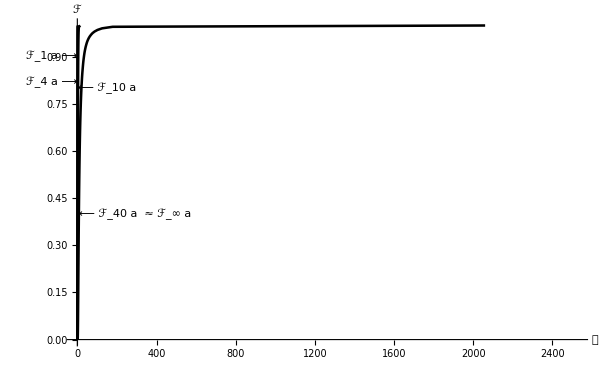

Exporting:./Figures/SimCDFsConverge

```mathematica
<<SimCDFsConvergePlot.m
```

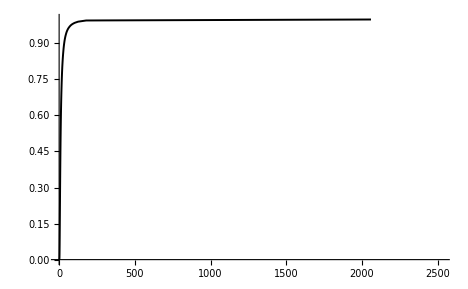

```mathematica
CDFPlots[[-1]]
```

```mathematica
Length[CDFatFuncList[[i]]]
```

Part::pkspec1: The expression i cannot be used as a part specification.

2

```mathematica
CDFatFuncList[[-1]][0.]
```

0.297797

```mathematica
CDFatFuncList[[-1]][0.99]
```

125.585

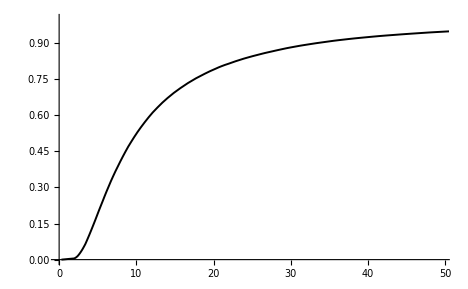

```mathematica
ParametricPlot[
         {CDFatFuncList[[-1]][CDFPoint],CDFPoint}
         ,{CDFPoint,0,0.999}
         ,PlotRange->{Automatic,Automatic}
         ,PlotStyle->{{Black,Thickness[.003]}}
         ,DisplayFunction->Identity
    ]
```

```mathematica
CDFatFuncList[[-1]][[2]]
```

```mathematica
CDFPlots[[-1]]
```

-Graphics-

```mathematica
SimCDFsConverge
```

-Graphics-

```mathematica
CDFatFuncList[[2]][0.94]
```

0.785201

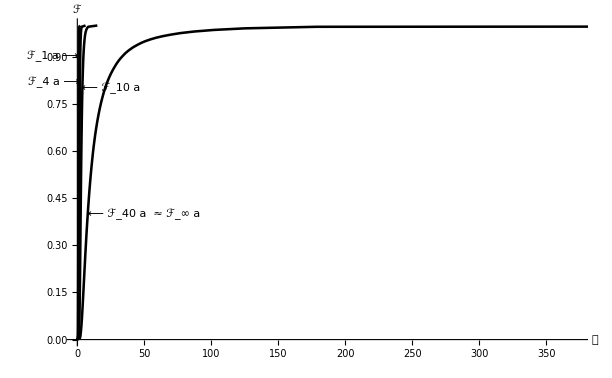

```mathematica
SimCDFsConverge = Show[
  CDFPlots[[2]]
, CDFPlots[[5]]
, CDFPlots[[11]]
, CDFPlots[[LastPeriod]]
  , Graphics[Text["\!\(\(ℱ\_1\%a\)\) ⟶",
  {CDFatFuncList[[2]][0.94], 0.9}, {1, 0}]]
  , Graphics[Text["\!\(\(ℱ\_4\%a\)\) ⟶",
  {CDFatFuncList[[5]][0.85], 0.82}, {1, 0}]]
, Graphics[Text[" ⟵ \!\(\(ℱ\_10\%a\) \)",
  {CDFatFuncList[[10]][0.8], 0.8}, {-1, 0}]]
, Graphics[Text[" ⟵ \!\(\(ℱ\_40\%a\) \) ≈ \!\(\(ℱ\_∞\%a\)\) ",
  {CDFatFuncList[[LastPeriod]][0.4], 0.4}, {-1, 0}]]
(*, DisplayFunction -> $DisplayFunction*)
, AxesLabel->{"𝒶","ℱ"}
, ImageSize  ->  FullPageSize
, AxesOrigin -> {0, 0}
, PlotRange -> {{0, CDFatList[[-1, -(Round[Length[CDFatList[[-1]]]/1000]+1)]]}, {0, 1}}
, DisplayFunction->$DisplayFunction
, BaseStyle -> {FontSize -> 14}
]
```

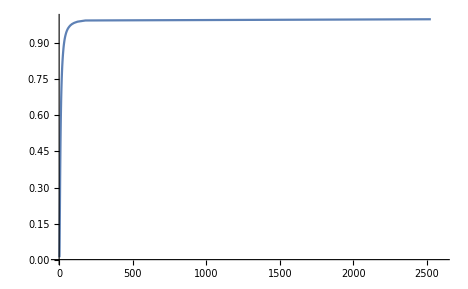

```mathematica
ParametricPlot[{CDFatFuncList[[-1]][p],p},{p,0.01,1.0}
,AxesOrigin->{0,0}
,PlotRange->{{0,2600},{0.,1.}}
]
```

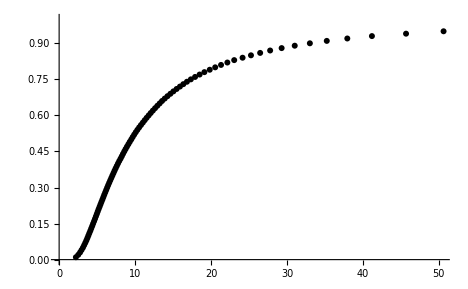

```mathematica
ListPlot[Table[{CDFatFuncList[[-2]][p],p},{p,0.01,1.0,0.01}]]
```

```mathematica
CDFatFuncList[[-1]][1.0]
```

2526.77

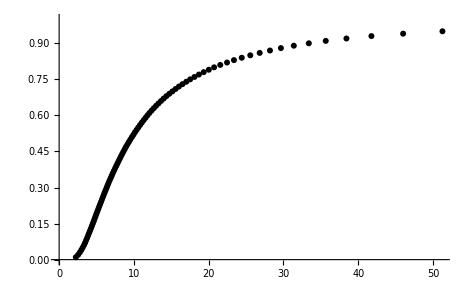
p -Graphics-

```mathematica
ListPlot[Table[{CDFptFuncList[[-1]][p],p},{p,0.01,1.0,0.01}]]p
```

```mathematica
CDFatFuncList[[-1]][0.5]
```

9.52866

```mathematica
CDFatFuncList[[-1]][0.5]
```

9.52866

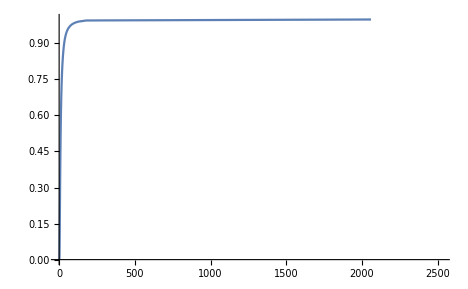

```mathematica
ParametricPlot[
{CDFatFuncList[[-1]][CDFPoint],CDFPoint}
,{CDFPoint,0,0.999}
,PlotRange->{{0.,CDFatList[[-1,-1]]},{0,1}}
         ]
```

```mathematica
CDFatList[[-1,-1]]
```

2526.77

```mathematica
SimCDFsConverge = Show[
  CDFPlots[[2]]
, CDFPlots[[5]]
, CDFPlots[[11]]
, CDFPlots[[LastPeriod]]
  , Graphics[Text["\!\(\(ℱ\_1\%a\)\) ⟶",
  {CDFatFuncList[[2]][0.94], 0.9}, {1, 0}]]
  , Graphics[Text["\!\(\(ℱ\_4\%a\)\) ⟶",
  {CDFatFuncList[[5]][0.85], 0.82}, {1, 0}]]
, Graphics[Text[" ⟵ \!\(\(ℱ\_10\%a\) \)",
  {CDFatFuncList[[10]][0.8], 0.8}, {-1, 0}]]
, Graphics[Text[" ⟵ \!\(\(ℱ\_40\%a\) \) ≈ \!\(\(ℱ\_∞\%a\)\) ",
  {CDFatFuncList[[LastPeriod]][0.4], 0.4}, {-1, 0}]]
(*, DisplayFunction -> $DisplayFunction*)
, AxesLabel->{"𝒶","ℱ"}
, ImageSize  ->  FullPageSize
, AxesOrigin -> {0, 0}
(*, PlotRange -> {{0, CDFatList[[-1, -(Round[Length[CDFatList[[-1]]]/1000]+1)]]}, {0, 1}}*)
, DisplayFunction->$DisplayFunction
, BaseStyle -> {FontSize -> 14}
]
```

-Graphics-

```mathematica
CDFatFuncList
```

{0,InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

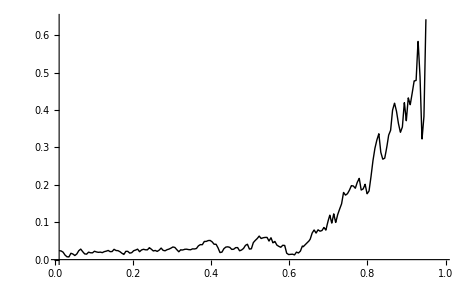

```mathematica
Plot[CDFatFuncList[[-1]][p]-CDFatFuncList[[-2]][p],{p,0.01,0.99}]
```

```mathematica
Length[atMean]
```

80

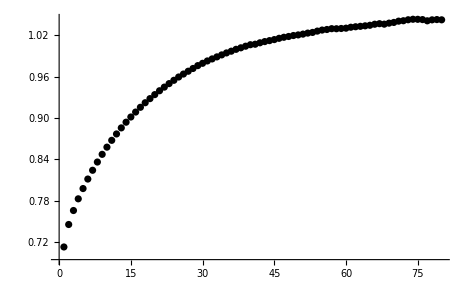

```mathematica
ListPlot[cLevtMean/pLevtMean]
```